```mathematica
Parameters
```

Parameters

```mathematica
αm=1;
αΛ=1;
αb=1;
αk=10^-10;
ασ=1;
αn=1;
```

```mathematica
Reference model
```

model Reference

```mathematica
Ωradref=9.26*10^-5;
Ωmref=0.315;
ΩΛref=1-Ωmref-Ωradref;
Ωbref=0.049;
fbref=Ωbref/Ωmref;
Ωkref=0;
href=0.674;
σ8ref=0.809;
nsref=0.965;
```

```mathematica
New cosmology
```

cosmology New

```mathematica
(* This generates parameters that give T = 2.725 K today *)
Ωrad=Ωradref/(Ωradref+αm Ωmref+αΛ ΩΛref+αk);
Ωm=(αm Ωmref)/(Ωradref+αm Ωmref+αΛ ΩΛref+αk);
ΩΛ=(αΛ ΩΛref)/(Ωradref+αm Ωmref+αΛ ΩΛref+αk);
fb=αb fbref;
Ωb=fb Ωm;
Ωk=αk/(Ωradref+αm Ωmref+αΛ ΩΛref+αk);
h=href √(Ωradref+αm Ωmref+αΛ ΩΛref+αk);
σ8=ασ σ8ref;
ns=αn nsref;
Print["Ωm - ",Ωm];
Print["Ωb - ",Ωb];
Print["ΩΛ - ",ΩΛ];
Print["Hubble Constant - ",100*h];
Print["Ωcdm - ",Ωm-Ωb];
Print["h-",h];
```

Ωm - 0.315

Ωb - 0.049

ΩΛ - 0.684907

Hubble Constant - 67.4

Ωcdm - 0.266

h-0.674

```mathematica
Star formation code
```

code formation Star

```mathematica
Integration method
```

Integration method

```mathematica
OneVarIntegrate[points_]:=Module[{total,dx,i},
total=0;
For[i=1,i≤Length[points]-1,i++,
dx=points[[i+1,1]]-points[[i,1]];
total=total+1/2(points[[i+1,2]]+points[[i,2]])*dx;
];
Return[total];
];
```

```mathematica
Modified SFR code
```

code Modified SFR

```mathematica
(* Note that the parameters must be chosen self-consistently to give T = 2.725 K today *)
posSFR[h_,Ωm_,Ωb_,ΩΛ_,Ωk_,σ8_,ns_]:=Module[{ΔN,k,tc,LogMmax,q,Q0,Λ,a,Hubble,G,G0,δc,Σ,S,ρvir,s,F,DiffF,LogM4,LogM6,LogM7,tswitch,SFR,P,f,ComptonCooling, IntegratedComptonRate,tcomp,EarlyCooling,Rate,DiffP,CoolingRate,CoolingPoints,LogMHor,teq,Mtyp,tcool,tgrav,LogMcool,Ωk0,Ωm0,nγ,ξm,ΩΛ0,H0,R0,ρeq,Teq,LogMeq,aeq,Meq,M8,aRfact,nscorr,fb,tlist,LogMmin,tmax,tmin,numt,numLogM,LogMlist,time,SFRPoints,approxFunction,w,tstart,tend,Mcrit,tpeak,tstop,SFRList,tfail,A,aflat,trec, β,temp,temp2,temp3,y,LogQ,m,eV,Mpc,second,km,meter,Gyr,kg,t,ttoday,LogM,Kelvin,tvir,cm,erg},
A=√(32/(3π));
f=.35;
k=-1;
fb=Ωb/Ωm;
q=10^LogQ;
Q0=2 10^-5;
Ωk0=Ωk;
Ωm0=Ωm;
nγ=4.104*10^8 m^-3;
ξm=(3 H0^2 Ωm)/nγ 3.370*10^11 eV/m^3;
ΔN=0;
H0=100h km/(second Mpc)Mpc/(3.09 10^22 meter) (1000meter)/km (3.15 10^16 second)/Gyr Gyr;
Λ=3 H0^2 ΩΛ;
y=Log10[((8π)/1.708^2)^-1 Λ]-120;
Teq=0.22ξm;
ρeq=(1+21/8(4/11)^(4/3))π^2/15(Teq/(1.22 10^28 eV))^4(5.39121 10^-44 second )^-2((3.15 10^16 second)/Gyr)^2 Gyr^2;
aeq=((3Ωm0)/(8π ρeq H0))^(1/3)ⅇ^ΔN/Ωk0^(1/2);
(*Σ is s(μ) in paper*)
Meq=1.18 10^17((3.727eV)/ξm);
M8=(4π)/3 ξm nγ (8 Mpc/h)^3(Mpc/(3.09 10^22 m))^-3(1.8*10^-36 kg)/eV*(1.988*10^30 kg)^-1;
aRfact=(((4π)/3 ξm nγ)^-1(Mpc/(3.09 10^22 m))^3((1.8*10^-36 kg)/eV)^-1(1.988*10^30 kg))^(1/3)(Mpc/h)^-1/.Mpc->1;
nscorr[LogM_]:=√((1-0.48(ns-0.98)(0.6+3Log10[Ωm h]+3Log10[aRfact] +LogM))(Ωm h)^(ns-0.98));
Σ[LogM_]:=nscorr[LogM]((9.1(10^LogM/Meq)^(-2/3))^(-.27)+(50.5Log[10,834+(10^LogM/Meq)^(-1/3)]-92)^(-.27))^(-1/.27); 
S[LogM_]:=(q Q0 Σ[LogM])^2;
a=g/.First[NDSolve[{g'[t]==√((8π ρeq aeq^4)/3 1/g[t]^2+(8π ρeq aeq^3)/3 1/g[t]+Λ/3 g[t]^2-k),g[0]==aeq},g,{t,0,50 √(3/Λ)}]];
teq=(√2-1)/(√(3π ρeq));
trec=0.000332;
Hubble[t_]:=a'[t]/a[t];
(************)
G=g /.First[NDSolve[{g''[t]+2Hubble[t]g'[t]==4π ρeq aeq^3/a[t]^3 g[t],g[0]==5/2,g'[0]==3/2 Hubble[0]},g,{t,0,50 √(3/Λ)}]];
ttoday=t/.FindRoot[H0-Hubble[t],{t,10}];
LogQ=x/.FindRoot[(σ8-√(S[Log10[M8]] G[t]^2)/.t->ttoday)/.LogQ->x,{x,0}];
δc[t_]:=1.686/G[t];
F[LogM_,t_]:=Erf[δc[t]/(√(2S[LogM]))];
DiffF[LogM_,t_]=Derivative[1,0][F][LogM,t];
aflat=g/.First[NDSolve[{g'[t]==√((8π ρeq aeq^4)/3 1/g[t]^2+(8π ρeq aeq^3)/3 1/g[t]+Λ/3 g[t]^2),g[0]==aeq},g,{t,0,50 √(3/Λ)}]];
(* Although not obvious from ts form, this fitting function taken from Tegmark et. al. has the correct scaling properties. *)ρvir[t_]:=Re[With[{x=(Λ aflat[t]^3)/(8 π ρeq aeq^3)}, Λ/(x 8π)(18 π^2+52.8 x^0.7+16x)]];
(*This is the mass corresponding to T=10^4 K, called Subscript[M, min] in the paper. *)
LogM4[t_]:=With[{kB=1.307 10^-23 (kg meter^2/second^2)/Kelvin(3.15 10^16 second/Gyr)^2,T=10^4 Kelvin,μ=.6 1.672 10^-27 kg,g= 6.673 10^-11 meter^3/(kg second^2)(3.15 10^16 second/Gyr)^2,Msun=2 10^30 kg},3/2 Log[10,3(kB T)/(μ .6)(3/(4π))^(1/3)Msun^(-2/3)g^(-2/3)( Gyr^-2)^(-1/3)Gyr^2 kg^(2/3) (meter^3/(Gyr^2 kg))^(2/3) ((1/Gyr^2)^(1/3))/meter^2]-1/2 Log[10,ρvir[t]]];
β[x_,tvir_,LogM_,t_]:=Piecewise[{{Erfc[(δc[tvir]-δc[t])/(√(2(S[x]-S[LogM])))],t>tvir>0}},0];
temp2[x_,tvir_,LogM_,t_]=Re[Derivative[1,1,0,0][β][x,tvir,LogM,t]];
DiffP[tvir_,LogM_,t_]:=NIntegrate[-10^(LogM-x)temp2[x,tvir,LogM,t],{x,LogM-Log[10,2],LogM}];
ComptonCooling[t_]:=With[{σ=6.65 10^-29 m^2,L=7.57 10^-16 kg m^2 s^-2 m^-3 (3.15 10^16 s/Gyr)^2(Kelvin)^-4,me= 9.1 10^-31 kg,c=3*10^8 m/s 3.15 10^16 s/Gyr,Tγ=Teq/(8.617 10^-5 eV/Kelvin)aeq/a[t]},((3me c)/(4 σ L Tγ^4))^-1 Gyr];
tcomp=x/.FindRoot[Abs[1/ComptonCooling[x]-x],{x,.9}];
tgrav[t_]:=1/(√ρvir[t]);
(*LogMcool is the log of what is called Subscript[M, max] in the paper*)
LogMcool[t_]:=With[{mp=1.672 10^-27 kg,λ=10^-23(erg cm^3)/second meter^3/(10^6 cm^3)( 3.15 10^16 second/Gyr)^3(kg meter^2/second^2)/(10^7 erg),g= 6.673 10^-11 meter^3/(kg second^2)(3.15 10^16 second/Gyr)^2,X=.76,Msun=2 10^30 kg},Log[10,(6/π)^(1/2)((fb X^2 λ)/(0.6 mp^2))^(3/2)g^(-5/2)(Msun)^-1(ρvir[t] Gyr^-2)^(1/4)(kg (meter^3/(Gyr^2 kg))^(5/2))/((1/Gyr^2)^(1/4) (meter^5/(Gyr^3 kg))^(3/2))]];
tmin[t_]:=If[(t≥2trec+teq)&&(2trec+teq≥x/.FindRoot[ Abs[f/A tgrav[x]-(t-x)],{x,t}]),0,Max[2trec+teq,x/.FindRoot[Abs[f/A tgrav[x]-(t-x)],{x,t}]]];
tmax[LogM_,t_]:=Which[LogM>LogMcool[t],
x/.FindRoot[Abs[LogMcool[x]-LogM],{x,t}],
LogM<LogM4[t],x/.FindRoot[Abs[LogM4[x]-LogM],{x,t}],True,t
];
(*tpeak, tstart, tend, and tfail make a rough guess at where the SFR will peak*)
tpeak=Min[5.32839975353552*(8π)/3 ρeq aeq^3,√(3/Λ), x/.FindRoot[Abs[1.686/(√2)-q Q0 G[x]Σ[LogM4[x]]],{x,.1}]];
tstart=.02tpeak;
tend=4tpeak;
tfail=Min[5.32839975353552*(8π)/3 ρeq aeq^3,√(3/Λ),x/.FindRoot[Abs[1.686/(√2)-q Q0 G[x]Σ[LogMcool[x]]],{x,tpeak}]];
CoolingRate[LogM_,t_]:=
Which[LogM>LogMcool[tcomp]&&tmin[t]<tcomp,OneVarIntegrate[Table[{tf,DiffP[tf,LogM,t](A fb)/tgrav[tf]},{tf,tmin[t],Min[tcomp,t],(Min[tcomp,t]-tmin[t])/10}]],
tmin[t]<tmax[LogM,t],OneVarIntegrate[Table[{tf,DiffP[tf,LogM,t](A fb)/tgrav[tf]},{tf,tmin[t],tmax[LogM,t],(tmax[LogM,t]-tmin[t])/10}]],True,0];
(*LogMmax and LogMmin define a range of integration for M.  They are NOT the same as Subscript[M, max] and Subscript[M, min] from the paper.  Adjust for accuracy/speed as desired*)
LogMmax[t_]:=x/.FindRoot[Abs[Σ[x]G[t]q Q0-1/3 1.686/(√2)],{x,10}];
LogMmin[t_]:=Min[LogM4[tmin[t]],LogMmax[t]-1];
(*This is where you must specify what times the SFR is integrated over.  Also, increasing the number of mass points is a good way to increase accuracy.*)
CoolingPoints=
Which[tfail<tcomp,
Union[
If[tend<tcomp,Flatten[Table[{l,m,CoolingRate[l,m]},{m,tend,1.5 tcomp,.01},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],{}],
If[tend<√(3/Λ),Flatten[Table[{l,m,CoolingRate[l,m]},{m,tend,10*tend,(9tend)/60},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],{}],If[10tend<√(3/Λ),Flatten[Table[{l,m,CoolingRate[l,m]},{m,10tend,√(3/Λ),(√(3/Λ)-10tend)/60},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],{}],Flatten[Table[{l,m,CoolingRate[l,m]},{m,tstart,tend,(tend-tstart)/120},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1]],
True,
Union[Flatten[Table[{l,m,CoolingRate[l,m]},{m,tstart,4tfail,(4tfail-tstart)/120},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],Flatten[Table[{l,m,CoolingRate[l,m]},{m,tstart,tend,(tend-tstart)/60},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],
If[10tfail<√(3/Λ),Flatten[Table[{l,m,CoolingRate[l,m]},{m,10tfail,√(3/Λ),(√(3/Λ)-10tfail)/60},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],{}],
If[tfail<√(3/Λ),Flatten[Table[{l,m,CoolingRate[l,m]},{m,4tfail,10*tfail,(6tfail)/60},{l,LogMmin[m],LogMmax[m],(LogMmax[m]-LogMmin[m])/20}],1],{}]
]
];
(*The following lines create a list of points.  Variable names are sloppily reused, but there should not be any conflict.*)
tlist=Flatten[Union[Take[CoolingPoints,All,{2,2}]]];
tmax=Max[tlist];
tmin=Min[tlist];
LogMlist=Flatten[Union[Take[CoolingPoints,All,{1,1}]]];
LogMmax=Max[LogMlist];
LogMmin=Min[LogMlist];
numt=Length[tlist];
numLogM=Length[LogMlist];
SFRPoints={};
If[numt==0,Continue[],0];
If[numLogM==0,Continue[],0];
For[w=1,w≤numt,w++,
time=tlist[[w]];
approxFunction=Union[Round[Drop[Select[Re[CoolingPoints],#[[2]]==time&],{},{2,2}],.00000001]];
AppendTo[SFRPoints,{time,OneVarIntegrate[Map[{#[[1]],#[[2]]*DiffF[#[[1]],time]}&,approxFunction]]}];
];
Print["****"];
Print["H0 : ",H0];
Print[{y,LogQ,ΔN}];
Print[{"tpeak ",tpeak}];
Print[{"tstart ",tstart}];
Print[{"tend ",tend}];
Print[{"tfail ",tfail}];
Print[{"tcomp ",tcomp}];
Print[{"G(today)",G[t]/.t->ttoday}];
Print["****"];
Return[SFRPoints];
]
```

```mathematica
Star formation rate
```

formation rate Star

```mathematica
(* Note that the parameters must be chosen self-consistently to give T = 2.725 K today *)
sfr=Quiet[posSFR[h,Ωm,Ωb,ΩΛ,Ωk,σ8,ns]];
```

****

H0 : 0.0687087

{-122.948,-0.0514782,0}

{tpeak ,2.1961}

{tstart ,0.043922}

{tend ,8.7844}

{tfail ,5.28927}

{tcomp ,0.901907}

{G(today),4060.33}

****

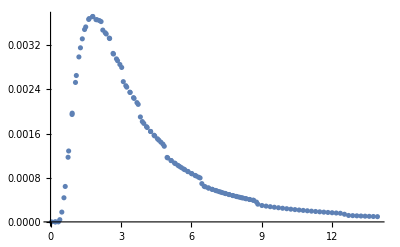

```mathematica
ListPlot[Select[sfr,#[[1]]<14&]]
```

```mathematica
par={αm,αΛ,αb,αk,ασ,αn};
```

```mathematica
SetDirectory["/Users/navonilsaha/Documents"];
Export["sfr-params-010(g).txt", par, "Table"];
Export["sfr-output-010(g).txt", sfr, "Table"];
```